```mathematica
Quit
```

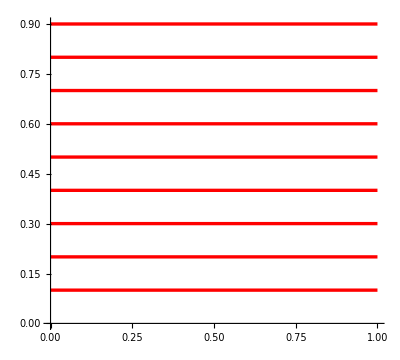

```mathematica
Table[{θ1,C1},{C1,1/10,9/10,1/10}];
Curve1=ParametricPlot[{%},{θ1,0,1},PlotStyle->Directive[Thickness[.006],Red]]
```

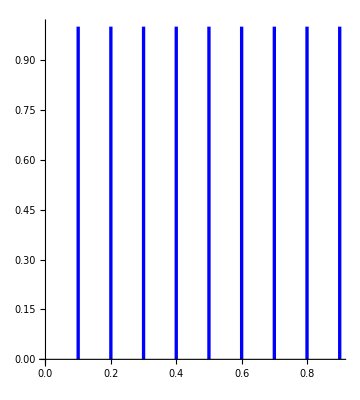

```mathematica
Table[{C2,θ2},{C2,1/10,9/10,1/10}];
Curve2=ParametricPlot[{%},{θ2,0,1},PlotStyle->Directive[Thickness[.006],Blue]]
```

```mathematica
Ref1=ParametricPlot[{X,Y},{X,0,1},{Y,0,1},PlotStyle->Directive[RGBColor[0.618,0.618,0.618]],Mesh->None,BoundaryStyle->Directive[Thickness[.008],Black],Axes->False,Frame->False,PerformanceGoal->"Quality"];
```

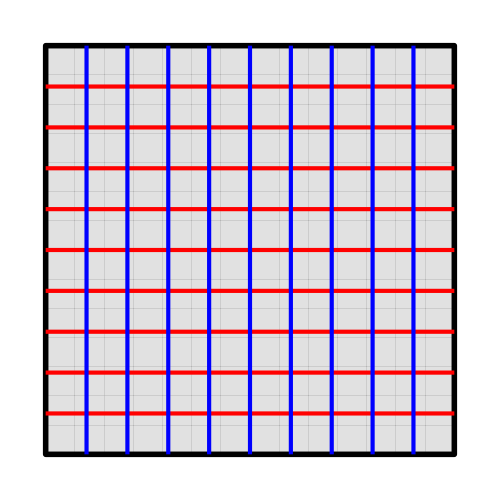

```mathematica
Show[Ref1,Curve1,Curve2,Boxed->False,Axes->False,ImageSize->500,PerformanceGoal->"Quality",MaxRecursion-> 10,ViewProjection->"Orthographic"]
```

```mathematica
XMax=2Pi;
YMax=5;
```

```mathematica
XLeft={θ1,0,XMax/2};
XRight={θ1,XMax/2,XMax};
YBot={θ2,0,YMax/2};
YTop={θ2,YMax/2,YMax};
```

```mathematica
x0[θ1_,θ2_]:=(1+θ2) Cos[θ1]+2/100 θ2^2 Cos[10θ1]
y0[θ1_,θ2_]:=(1+θ2)Sin[θ1]+2/100 θ2^2 Sin[10θ1]
z0[θ1_,θ2_]:=12-1/2 (8/2-θ2)^2
```

```mathematica
a=2;
b=2;
c=4;
```

```mathematica
Curve1=ParametricPlot3D[Table[{x0[X,Y0],y0[X,Y0],z0[X,Y0]},{Y0,1/10 5,9/10 5,1/10 5}],{X,0,2Pi},PlotStyle->Directive[Thickness[.005],Red],PerformanceGoal->"Quality",MaxRecursion-> 10]
```

-Graphics3D-

```mathematica
Curve2=ParametricPlot3D[Table[{x0[X0,Y],y0[X0,Y],z0[X0,Y]},{X0,1/10 2Pi,9/10 2Pi,1/10 2Pi}],{Y,0,5},PlotStyle->Directive[Thickness[.005],Blue],PerformanceGoal->"Quality",MaxRecursion-> 10]
```

-Graphics3D-

```mathematica
Bound1=ParametricPlot3D[Evaluate[{{x0[θ1,θ2],y0[θ1,θ2],z0[θ1,θ2]}/.{θ2->YMax}}],Evaluate[XRight],Evaluate[YTop],PlotRange->All,BoundaryStyle->Directive[Thickness[.008],Black],PerformanceGoal->"Quality",MaxRecursion-> 5];
Bound2=ParametricPlot3D[Evaluate[{{x0[θ1,θ2],y0[θ1,θ2],z0[θ1,θ2]}/.{θ2->YMax}}],Evaluate[XLeft],Evaluate[YTop],PlotRange->All,BoundaryStyle->Directive[Thickness[.008],Black],PerformanceGoal->"Quality",MaxRecursion-> 5];
Bound3=ParametricPlot3D[Evaluate[{{x0[θ1,θ2],y0[θ1,θ2],z0[θ1,θ2]}/.{θ2->0}}],Evaluate[XLeft],Evaluate[YBot],PlotRange->All,BoundaryStyle->Directive[Thickness[.008],Black],PerformanceGoal->"Quality",MaxRecursion-> 5];
Bound4=ParametricPlot3D[Evaluate[{{x0[θ1,θ2],y0[θ1,θ2],z0[θ1,θ2]}/.{θ2->0}}],Evaluate[XRight],Evaluate[YBot],PlotRange->All,BoundaryStyle->Directive[Thickness[.008],Black],PerformanceGoal->"Quality",MaxRecursion-> 5];
```

去掉反光

```mathematica
Manipulate[ParametricPlot3D[{x0[X,Y],y0[X,Y],z0[X,Y]},{X,0,2Pi},{Y,0,5},PlotStyle->Directive[RGBColor[0.618,0.618,1],Opacity[0.8]],Mesh->None,BoundaryStyle->Directive[Thickness[.008],Black],Boxed->False,Axes->False,PerformanceGoal->"Quality",ViewProjection->"Orthographic",(*ColorFunction->White,*)Lighting->{{"Point",White,{1,0,1}},{"Directional",RGBColor[1,1,1],{a,b,c},{{,0,0}}}},MaxRecursion-> 10],{a,-10,10},{b,-50,10},{c,-10,50}]
```

```mathematica
Cur1=ParametricPlot3D[{x0[X,Y],y0[X,Y],z0[X,Y]},{X,0,2Pi},{Y,0,5},PlotStyle->Directive[RGBColor[0.618,0.618,1],Opacity[0.8]],Mesh->None,Boxed->False,Axes->False,PerformanceGoal->"Quality",ViewProjection->"Orthographic",(*ColorFunction->White,*)Lighting->{{"Point",White,{1,0,1}},{"Directional",RGBColor[1,1,1],{10,-50,50},{{0,0,0}}}},MaxRecursion-> 10];
Show[Bound1,Bound2,Bound3,Bound4,Cur1,Curve1,Curve2,Boxed->False,Axes->False,ImageSize->800,PerformanceGoal->"Quality",MaxRecursion-> 10]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["Cur.png",Cur1,Background->None]
```

Cur.png